```mathematica
1+1
```

2

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(om/a^3+(1-om) F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

om/(a^3 (om/a^3+(1-om) F[a]))

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.3;γ0=0.52;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-5.39458×10^-9}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set1=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-2.82213},{-0.045,-2.97263},{-0.04,-3.12313},{-0.035,-3.27362},{-0.03,-3.42412},{-0.025,-3.57462},{-0.02,-3.72511},{-0.015,-3.87561},{-0.01,-4.02611},{-0.005,-4.1766},{0.,-4.3271},{0.005,-4.4776},{0.01,-4.62809},{0.015,-4.77859},{0.02,-4.92909},{0.025,-5.07958},{0.03,-5.23008},{0.035,-5.38058},{0.04,-5.53107},{0.045,-5.68157},{0.05,-5.83207}}

```mathematica
Y1=Interpolation[%]
```

InterpolatingFunction[…]

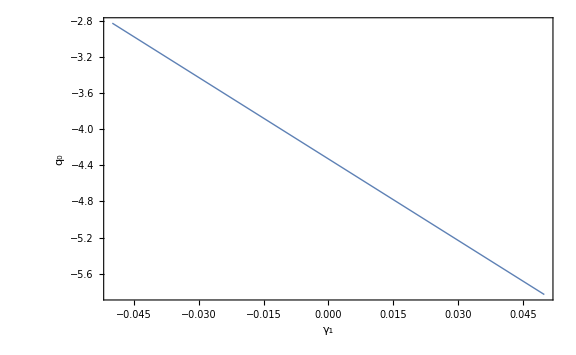

```mathematica
pl1=Plot[Y1[z],{z,-0.05,0.05},Frame->True,Axes->False,AxesLabel->{Style["γ_1", Black, FontSize->20], Style["q_0", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.3;γ0=0.59;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set3=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,0.412969},{-0.045,0.379526},{-0.04,0.346082},{-0.035,0.312638},{-0.03,0.279194},{-0.025,0.245751},{-0.02,0.212307},{-0.015,0.178863},{-0.01,0.14542},{-0.005,0.111976},{0.,0.0785323},{0.005,0.0450886},{0.01,0.0116449},{0.015,-0.0217987},{0.02,-0.0552424},{0.025,-0.0886861},{0.03,-0.12213},{0.035,-0.155574},{0.04,-0.189017},{0.045,-0.222461},{0.05,-0.255905}}

```mathematica
Y3=Interpolation[%]
```

InterpolatingFunction[…]

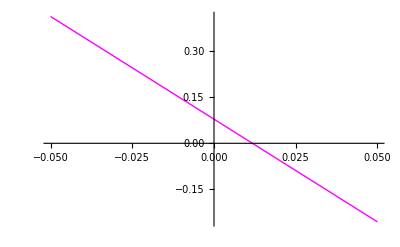

```mathematica
pl3=Plot[Y3[z],{z,-0.05,0.05},PlotStyle->{Thick,Magenta}]
```

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.3;γ0=0.55;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,F[a]} = {0.5,-8.3297×10^-10}.

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set2=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-0.329635},{-0.045,-0.389834},{-0.04,-0.450033},{-0.035,-0.510231},{-0.03,-0.57043},{-0.025,-0.630629},{-0.02,-0.690827},{-0.015,-0.751026},{-0.01,-0.811224},{-0.005,-0.871423},{0.,-0.931622},{0.005,-0.99182},{0.01,-1.05202},{0.015,-1.11222},{0.02,-1.17242},{0.025,-1.23261},{0.03,-1.29281},{0.035,-1.35301},{0.04,-1.41321},{0.045,-1.47341},{0.05,-1.53361}}

```mathematica
Y2=Interpolation[%]
```

InterpolatingFunction[…]

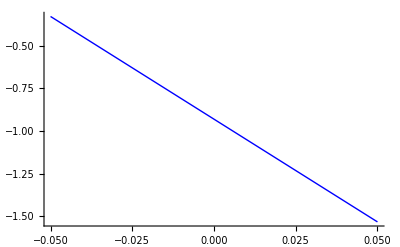

```mathematica
pl2=Plot[Y2[z],{z,-0.05,0.05},PlotStyle->{Thick,Blue}]
```

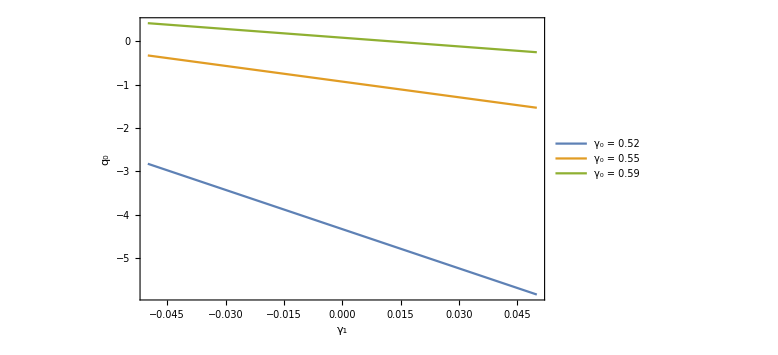

```mathematica
Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},Frame->True,Axes->False,FrameLabel->{Style["γ_1",Black,14],Style["q_0",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10},PlotLegends->Placed[LineLegend[{
"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"
},LabelStyle->{FontSize->10}],{0.8,0.4}]]
```

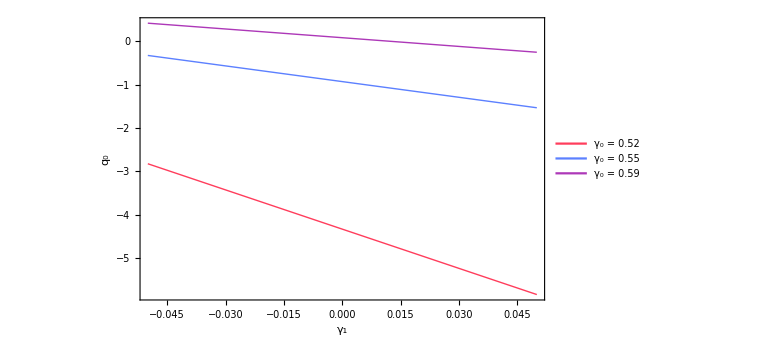

```mathematica
finalplot1=Plot[{Y1[z],Y2[z],Y3[z]},{z,-0.05,0.05},PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0 = 0.52","γ_0 = 0.55","γ_0 = 0.59"}, Background->White],{Left,Bottom}], Axes->False]
```

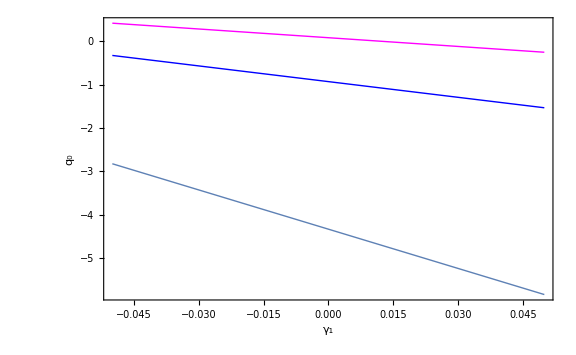

```mathematica
Show[pl1,pl2,pl3,PlotRange->All,Frame->True,FrameLabel->{"γ_1","q_0"},Axes->False]
```

```mathematica
Show[pl1,pl2,pl3, Frame->True,Axes->False,AxesLabel->{Style["γ_1", Black, FontSize->20], Style["q_0", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

-Graphics-

```mathematica
LogLogPlot[{flux[z,1],flux[z,0.496],flux[z,0.405],flux[z,0.354]} ,{z,0.1,20},PlotRange->All,PlotStyle->{{Dashed,Black},{Thick,Magenta},{Thick,Blue},{Thick,Red}},Frame->True,FrameLabel->{Style["E[keV]",Black,14],Style["E F_E[erg/(cm^2 sec)]",Black,14]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)20,Black],ImageSize->Large,PlotLegends->Placed[LineLegend[{
"ϵ = 0","ϵ = 0.5","ϵ = 1","ϵ = 1.5"
},LabelStyle->{FontSize->10}],{0.75,0.25}]]
```

-Graphics-

```mathematica
(* Compute the allowed range for gamma prime *)
```

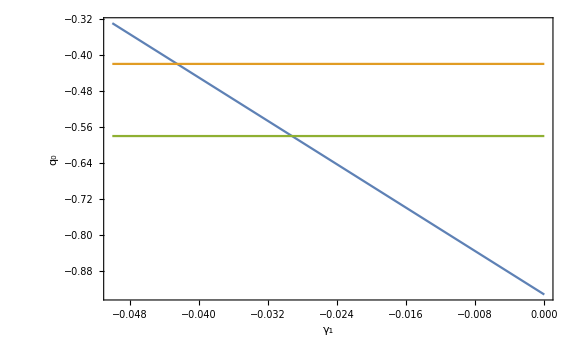

```mathematica
Plot[{Y2[z],-0.5+0.08,-0.5-0.08},{z,-0.05,0},Frame->True,Axes->False,FrameLabel->{Style["γ_1",Black,14],Style["q_0",Black,14]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10}]
```

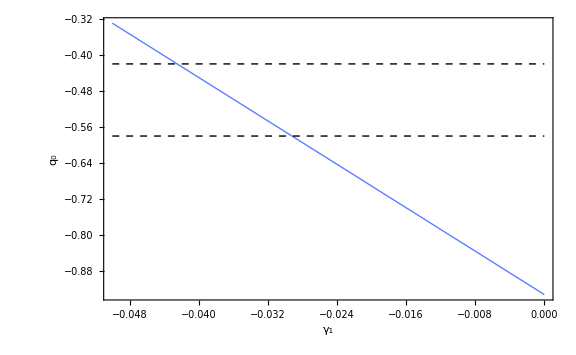

```mathematica
finalplot2=Plot[{Y2[z],-0.5+0.08,-0.5-0.08},{z,-0.05,0},PlotStyle->{{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, Black}, {Thick, Dashed, Black}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["γ_1", Black, FontSize->24, FontFamily->"Helvetica"],Style["q_0", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False]
```

```mathematica
Clear[z]
```

```mathematica
FindRoot[Y2[z]==-0.5+0.08,{z,-0.041}]
```

{z→-0.0424945}

```mathematica
FindRoot[Y2[z]==-0.5-0.08,{z,-0.03}]
```

{z→-0.0292051}

```mathematica
(* View solution for one extreme *)
```

```mathematica
om
```

0.3

```mathematica
γ0
```

0.55

```mathematica
γ1=-0.0424945;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

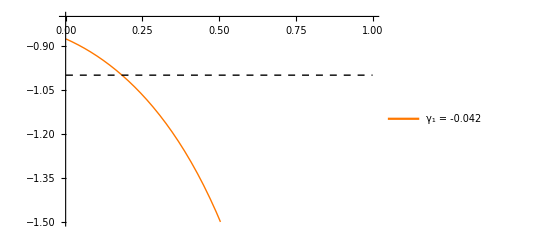

```mathematica
plw1=Plot[{w[z],-1},{z,0.001,1},PlotRange->{-1.5,-0.8},PlotStyle->{{Thick,RGBColor[1,0.47,0]},{Black,Dashed, Thick}}, PlotLegends->Placed[LineLegend[{"γ_1 = -0.042"}, Background->White],{Left,Bottom}], LabelStyle->{FontSize->16}]
```

```mathematica
(* Analytic expression: Fitting with polynomials *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.01,1,0.01}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.22026-0.859156 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(1.75363-0.666667 z)/(-1.4203+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

1.00286+0.41965 z-1.26614 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(0.681581+0.887626 z-0.333333 z^2)/(-0.792061-0.331439 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.986425+0.61024 z-1.73556 z^2+0.309846 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(-2.5271-5.04724 z+2.86712 z^2)/(3.1836+1.96949 z-5.60137 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

1.00254+0.304691 z-0.389954 z^2-1.75567 z^3+1.02253 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-0.881128-0.452892 z-1.58986 z^2+1.33333 z^3+0.333333 z^4)/(0.980454+0.297977 z-0.381361 z^2-1.71698 z^3+1. z^4)

```mathematica
Dif[z_]:=1-w5[z]/w[z]
```

```mathematica
Res=Table[{z,Dif[z]},{z,0.01,1.0,0.01}];
```

```mathematica
plotRes=ListPlot[Res]
```

-Graphics-

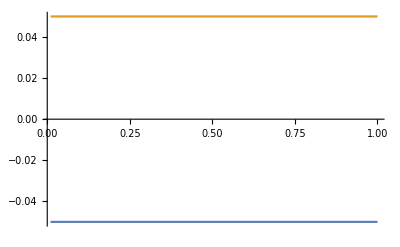

```mathematica
bounds=Plot[{-0.05,0.05},{x,0.01,1}]
```

```mathematica
Show[bounds,plotRes,PlotRange->All]
```

-Graphics-

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999523+0.388601 z-0.959982 z^2-0.262034 z^3-0.63694 z^4+0.657216 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(-1.32375-1.36798 z+0.0881901 z^2-1.2922 z^3+1.34362 z^4+0.666667 z^5)/(1.52084+0.591283 z-1.46068 z^2-0.398703 z^3-0.969147 z^4+1. z^5)

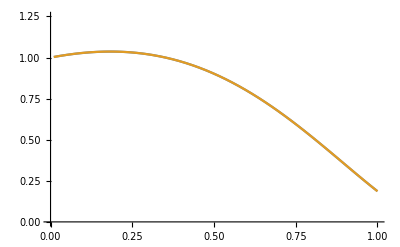

```mathematica
Plot[{Fz[z],P5},{z,0.01,1},PlotRange->{0,1.25}]
```

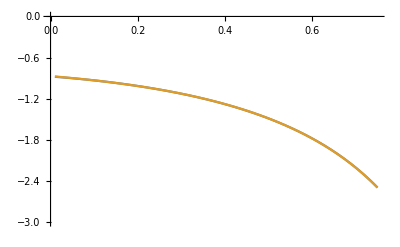

```mathematica
Plot[{w[z],w5[z]},{z,0.01,0.75},PlotRange->{-3,0}]
```

```mathematica
(* View solution for the other extreme *)
```

```mathematica
γ1=-0.0292051;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

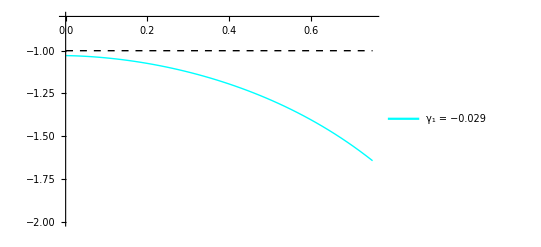

```mathematica
plw2=Plot[{w[z],-1},{z,0.001,0.75},PlotRange->{-2,-0.8},PlotStyle->{{Thick,Cyan},{Black,Dashed, Thick}}, PlotLegends->Placed[LineLegend[{"γ_1 = −0.029"}, Background->White],{Left,Bottom}], LabelStyle->{FontSize->16}]
```

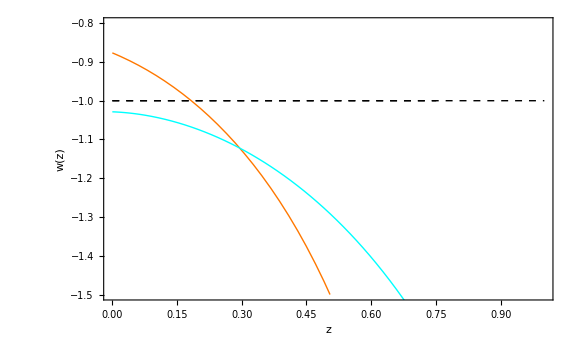

```mathematica
Show[plw1,plw2,PlotRange->{-1.5,-0.8},Frame->True,FrameLabel->{Style["z",Black,14],Style["w(z)",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],Axes->False,ImageSize->Large]
```

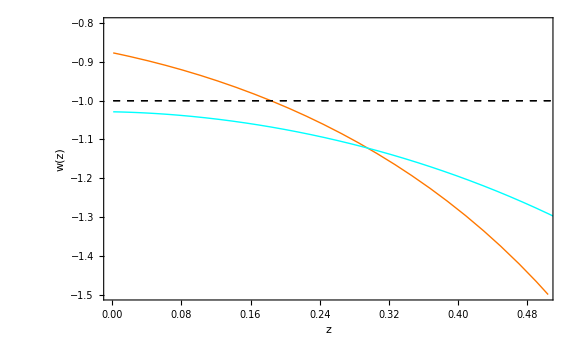

```mathematica
finalplot3=Show[plw1,plw2,PlotRange->{{0,0.5},{-1.5,-0.8}},ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24, FontFamily->"Helvetica"],Style["w(z)", Black, FontSize->24, FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, Axes->False]
```

```mathematica
Show[{w2[z],-1,w1[z]},{z,0.001,0.9},PlotRange->{-2,0},Frame->True,Axes->False,FrameLabel->{Style["z",Black,14],Style["w(z)",Black,15]},FrameStyle-> True,LabelStyle->Directive[Bold, (*Medium*)18,Black],ImageSize->Large,LabelStyle->{FontSize->10},LabelStyle->{FontSize->10}]
```

Show::gcomb: Could not combine the graphics objects in Show[{(0.681581+0.887626 z-0.333333 z^2)/(-0.792061-0.331439 z+1. z^2),-1,(1.75363-0.666667 z)/(-1.4203+1. z)},{z,0.001,0.9},PlotRange→{-2,0},Frame→True,Axes→False,FrameLabel→{z,w(z)},FrameStyle→True,LabelStyle→Directive[Bold,18,GrayLevel[0]],ImageSize→Large,LabelStyle→{FontSize→10},«1»].

Show[{(0.681581+0.887626 z-0.333333 z^2)/(-0.792061-0.331439 z+1. z^2),-1,(1.75363-0.666667 z)/(-1.4203+1. z)},{z,0.001,0.9},PlotRange→{-2,0},Frame→True,Axes→False,FrameLabel→{z,w(z)},FrameStyle→True,LabelStyle→Directive[Bold,18,GrayLevel[0]],ImageSize→Large,LabelStyle→{FontSize→10},LabelStyle→{FontSize→10}]

```mathematica
(* Fitting *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.01,1.0,0.01}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.0854-0.510737 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(2.4585-0.666667 z)/(-2.12517+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

0.993822+0.0279582 z-0.533361 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(1.84585+0.701613 z-0.333333 z^2)/(-1.86332-0.0524188 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.994778+0.0168845 z-0.506087 z^2-0.0180028 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(54.9443+19.3664 z-8.37055 z^2)/(-55.257-0.937885 z+28.1117 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

0.999756-0.0774773 z-0.0905265 z^2-0.65589 z^3+0.315786 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-3.24771-0.0275486 z-1.98145 z^2+1.33333 z^3+0.333333 z^4)/(3.16593-0.245347 z-0.28667 z^2-2.07701 z^3+1. z^4)

```mathematica
Dif[z_]:=1-w3[z]/w[z]
```

```mathematica
Dif[z_]:=1-w4[z]/w[z]
```

```mathematica
Res=Table[{z,Dif[z]},{z,0.01,1.0,0.01}];
```

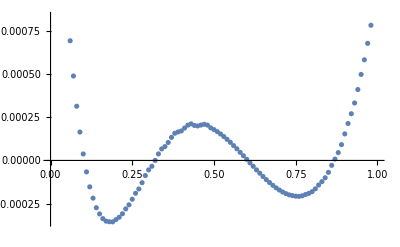

```mathematica
plotRes=ListPlot[Res]
```

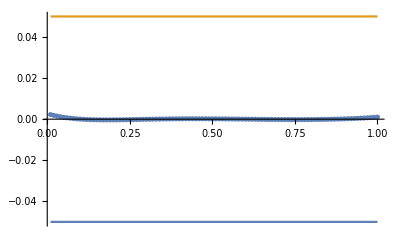

```mathematica
Show[bounds,plotRes,PlotRange->All]
```

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999894-0.081321 z-0.064415 z^2-0.72431 z^3+0.391802 z^4-0.0301053 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(34.1137-0.374374 z+23.346 z^2-17.3525 z^3-2.67146 z^4+0.666667 z^5)/(-33.2132+2.70122 z+2.13966 z^2+24.0592 z^3-13.0144 z^4+1. z^5)

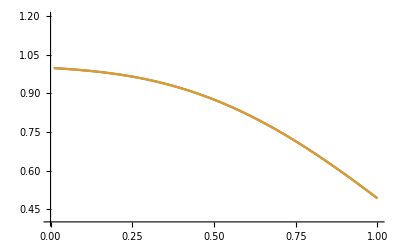

```mathematica
Plot[{Fz[z],P4},{z,0.01,1},PlotRange->{0.4,1.2}]
```

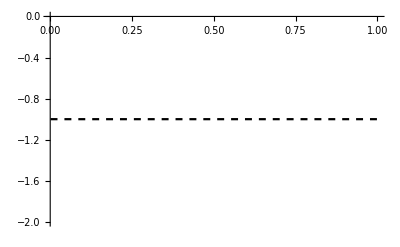

```mathematica
line=Plot[-1,{z,0.001,1},PlotStyle->{Dashed,Black}]
```

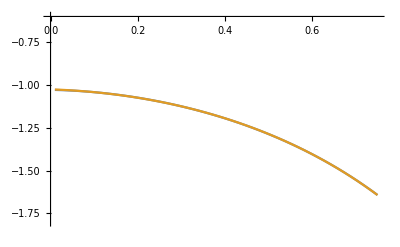

```mathematica
Plot[{w[z],w4[z]},{z,0.01,0.75},PlotRange->{-1.8,-0.6}]
```

```mathematica
Show[pl3,line]
```

-Graphics-

```mathematica
(* Impact of γ1 on q(z) and w(z) *)
```

```mathematica
Clear[γ1,w,q]
```

```mathematica
γ1=-0.04;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

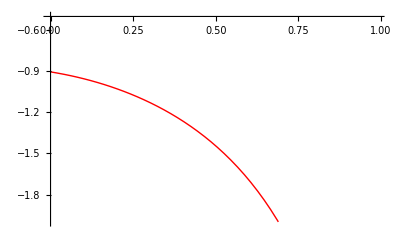

```mathematica
plot1=Plot[w[z],{z,0.001,0.99},PlotRange->{-2,-0.5},PlotStyle->{Thick,Red}]
```

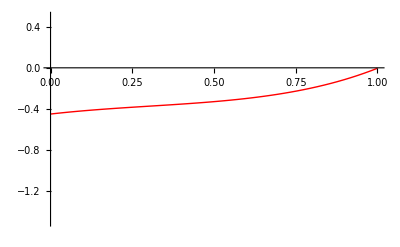

```mathematica
plot2=Plot[q[z],{z,0.001,1},PlotRange->{-1.5,0.5},PlotStyle->{Thick,Red}]
```

```mathematica
Clear[γ1]
```

```mathematica
γ1=-0.02;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol2=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol2];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

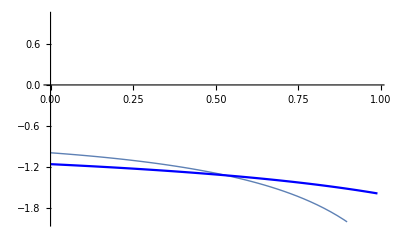

```mathematica
plot2=Plot[{w2[z],w1[z]},{z,0.001,0.99},PlotRange->{-2,1},PlotStyle->{Thick,Blue}]
```

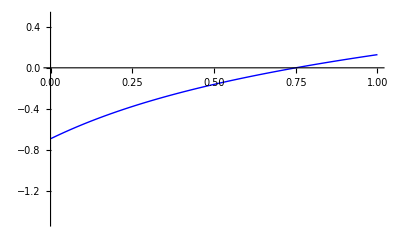

```mathematica
plot4=Plot[q[z],{z,0.001,1},PlotRange->{-1.5,0.5},PlotStyle->{Thick,Blue}]
```

```mathematica
γ1=0.02;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol3=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol3];Fz[z_]:=Fa[1/(1+z)];w3[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q3[z_]:=-1+((1+z) hz'[z])/hz[z];
```

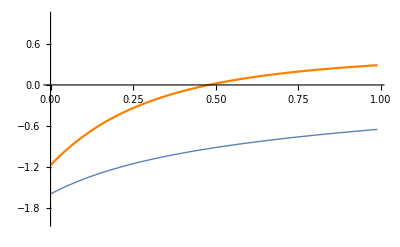

```mathematica
plot5=Plot[{w3[z],q3[z]},{z,0.001,0.99},PlotRange->{-2,1},PlotStyle->{Thick,Orange}]
```

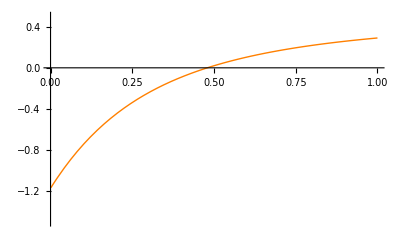

```mathematica
plot6=Plot[q[z],{z,0.001,1},PlotRange->{-1.5,0.5},PlotStyle->{Thick,Orange}]
```

```mathematica
γ1=0.04;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol4=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol4];Fz[z_]:=Fa[1/(1+z)];w4[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q4[z_]:=-1+((1+z) hz'[z])/hz[z];
```

```mathematica
plot7=Plot[{[z],w3[z]},{z,0.001,0.99},PlotRange->{-2,1},PlotStyle->{Thick,Magenta}]
```

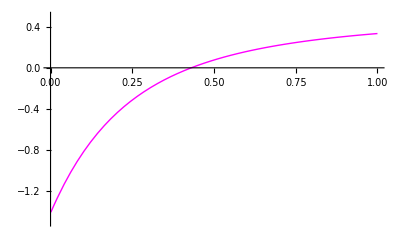

```mathematica
plot8=Plot[q[z],{z,0.001,1},PlotRange->{-1.5,0.5},PlotStyle->{Thick,Magenta}]
```

```mathematica
Show[plot1,plot3,plot5,plot7,PlotRange->{-2,0},Frame->True,FrameLabel->{"z","w(z)"},Axes->False]
```

Show::gcomb: Could not combine the graphics objects in Show[,plot3,,plot7,PlotRange→{-2,0},Frame→True,FrameLabel→{z,w(z)},Axes→False].

Show[-Graphics-,plot3,-Graphics-,plot7,PlotRange→{-2,0},Frame→True,FrameLabel→{z,w(z)},Axes→False]

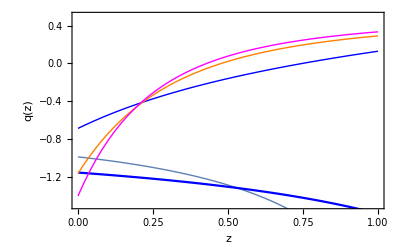

```mathematica
Show[plot2,plot4,plot6,plot8,PlotRange->{-1.5,0.5},Frame->True,FrameLabel->{"z","q(z)"},Axes->False]
```

```mathematica
(* Formato potencial *)
```

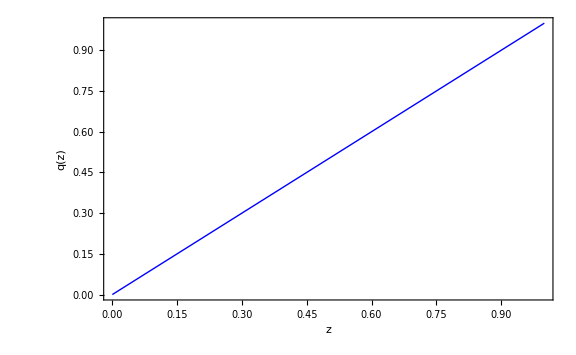

```mathematica
plot1=Plot[z,{z,0,1},FrameLabel->{Style["z",Black,14],Style["q(z)",Black,14]},Frame-> True,LabelStyle->Directive[Bold, (*Medium*)20,Black],ImageSize->Large,PlotStyle->{Thick,Blue}]
```

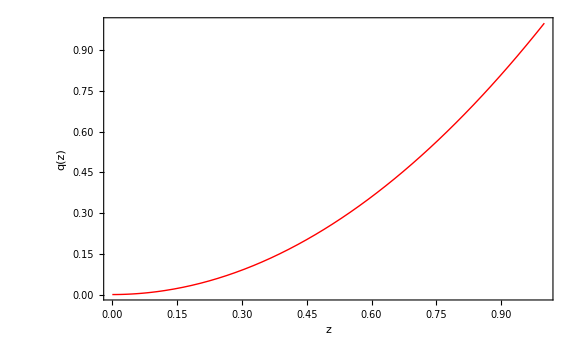

```mathematica
plot2=Plot[z^2,{z,0,1},FrameLabel->{Style["z",Black,14],Style["q(z)",Black,14]},Frame-> True,LabelStyle->Directive[Bold, (*Medium*)20,Black],ImageSize->Large,PlotStyle->{Thick,Red}]
```

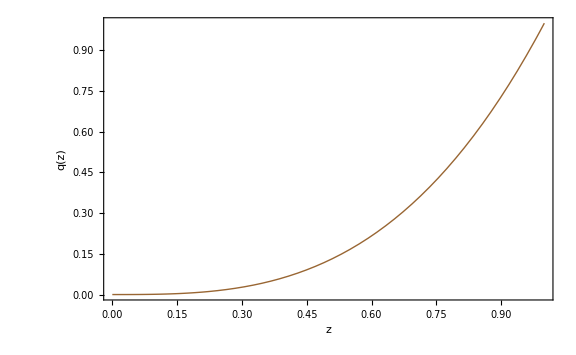

```mathematica
plot3=Plot[z^3,{z,0,1},FrameLabel->{Style["z",Black,14],Style["q(z)",Black,14]},Frame-> True,LabelStyle->Directive[Bold, (*Medium*)20,Black],ImageSize->Large,PlotStyle->{Thick,Brown}]
```

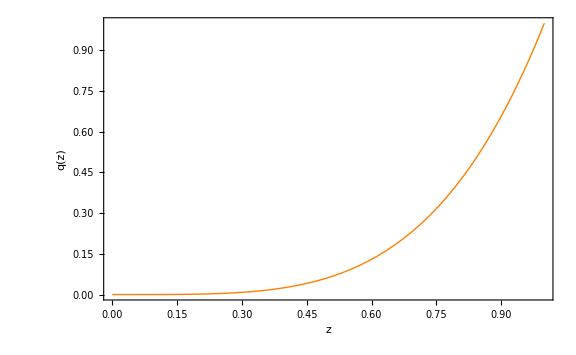

```mathematica
plot4=Plot[z^4,{z,0,1},FrameLabel->{Style["z",Black,14],Style["q(z)",Black,14]},Frame-> True,LabelStyle->Directive[Bold, (*Medium*)20,Black],ImageSize->Large,PlotStyle->{Thick,Orange}]
```

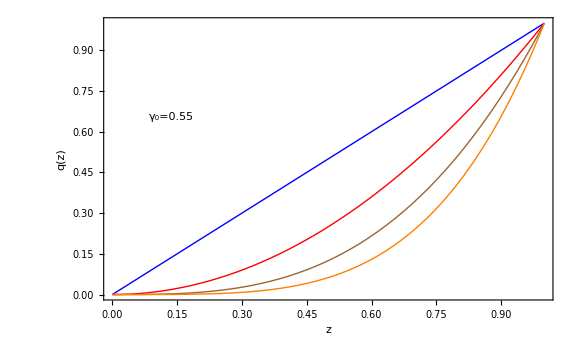

```mathematica
Show[plot1,plot2,plot3,plot4,Epilog->Inset[Framed[Column[{"γ_0=0.55",LineLegend[{Orange},{StringJoin[{"γ_1=-0.04"}]},LegendMarkerSize->{16,5}],LineLegend[{Brown},{StringJoin[{"γ_1=-0.02"}]},LegendMarkerSize->{16,5}],LineLegend[{Red},{StringJoin[{"γ_1=0.02"}]},LegendMarkerSize->{16,5}],LineLegend[{Blue},{StringJoin[{"γ_1=0.04"}]},LegendMarkerSize->{16,5}]}],RoundingRadius->10],Scaled[{0.15,0.65}]]]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\plots_paper"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\plots_paper

```mathematica
Export["q_0VSgamma1.pdf",finalplot1,ImageResolution->500]
```

q_0VSgamma1.pdf

```mathematica
Export["q_0VSgamma1_Bounds.pdf",finalplot2,ImageResolution->500]
```

q_0VSgamma1_Bounds.pdf

```mathematica
Export["w(z)_Extremes.pdf",finalplot3,ImageResolution->500]
```

w(z)_Extremes.pdf